```mathematica
trikotnik=Trikotnik[{0,0},{5,1},{7,4}]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
{Daljica[{0,0},{5,1}], Daljica[{5,1},{7,4}], Daljica[{7,4}, {0,0}]}
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{7,4},{0,0}]}

```mathematica
Stranice[Trikotnik[AA_,BB_,CC_]]:={Daljica[AA, BB], Daljica[BB, CC], Daljica[CC, AA]}
```

```mathematica
Stranice[trikotnik]
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{7,4},{0,0}]}

```mathematica
Koti[Trikotnik[AA_,BB_,CC_]]:={Kot[CC, AA, BB], Kot[AA, BB, CC], Kot[BB, CC, AA]}
```

```mathematica
Koti[trikotnik]/Degree//N
```

{18.4349,135.,26.5651}

```mathematica
Kot[AA_, BB_, CC_]:=ArcCos[(AA -BB).(CC -BB)/(Norm[AA -BB] Norm[CC -BB])]
```

```mathematica
AA ={0,0}
BB ={5,1}
CC={7,4}
```

{0,0}

{5,1}

{7,4}

```mathematica
(AA -BB).(CC -BB)/(Norm[AA -BB] Norm[CC -BB])
```

-1/(√2)

```mathematica
CC -BB
```

{2,3}

```mathematica
{1,2}.{3,4}
```

11

```mathematica
Norm[BB]//N
```

5.09902

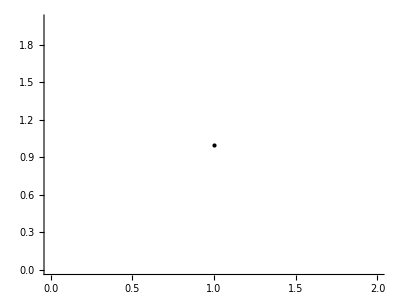

```mathematica
Graphics[Point[{1,1}], Axes->True]
```

```mathematica
Trikotnik[{0,0},{5,1},{7,4}]
```

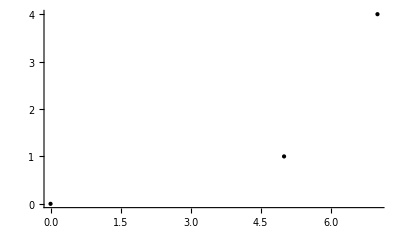

```mathematica
Graphics[{Point[{0,0}],Point[{5,1}],Point[{7,4}]}, Axes->True]
```

```mathematica
SlikaOglisc[Trikotnik[AA_,BB_,CC_]] := {Point[AA], Point[BB], Point[CC]}
```

```mathematica
Graphics[SlikaOglisc[trikotnik]]
```

-Graphics-

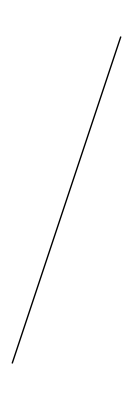

```mathematica
Graphics[Line[{{0,0}, {1,3}}], Axes->Automatic]
```

```mathematica
SlikaStranic[Trikotnik[AA_,BB_,CC_]] := {Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}]}
```

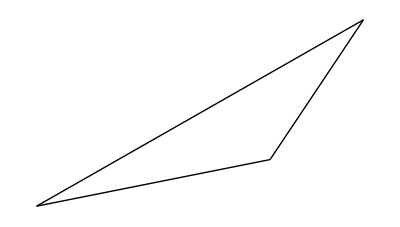

```mathematica
Graphics[SlikaStranic[trikotnik]]
```

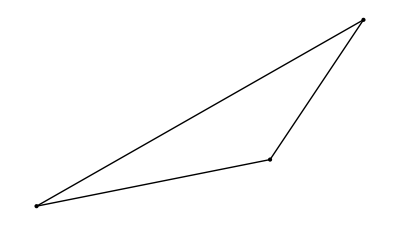

```mathematica
Graphics[{SlikaOglisc[trikotnik], SlikaStranic[trikotnik]}]
```

```mathematica
ClearAll[NarisiTrikotnik]
NarisiTrikotnik[trikotnik_Trikotnik] :=Graphics[{SlikaOglisc[trikotnik], SlikaStranic[trikotnik]}, Axes->True]
```

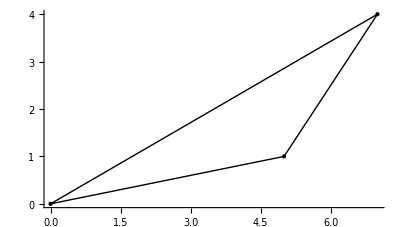

```mathematica
NarisiTrikotnik[trikotnik]
```

```mathematica
NarisiTrikotnik[3]
```

NarisiTrikotnik[3]